```mathematica
data=Import["XYlarge.dat","Data"];
```

```mathematica
data=SortBy[data,Last];
```

```mathematica
X1=Select[data,#[[3]]==0&][[;;,{1,2}]];
X2=Select[data,#[[3]]==1&][[;;,{1,2}]];
Y=data[[;;,3]];
X=data[[;;,{1,2}]];
```

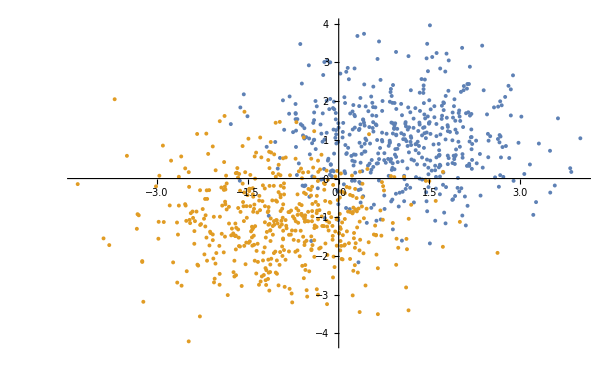

```mathematica
ListPlot[{X1,X2}]
```

```mathematica
g[z_]:=(1+Exp[-z])^-1
```

```mathematica
a[x_,w_]:=g[w.x]
```

```mathematica
x1x2=Flatten@Table[x1^(i-j)x2^j,{i,0,4},{j,0,i}];
```

```mathematica
L:=1/Length[data](Sum[Y[[i]]Log[a[XX[[i]],#1]+0.00001]+(1-Y[[i]])Log[1.000001-a[XX[[i]],#1]],{i,1,Length[data]}]-#2Sum[(#1[[i]])^2,{i,1,Length[#1]}])&
```

```mathematica
XX=Table[Flatten@Table[X[[k,1]]^(i-j)X[[k,2]]^j,{i,0,4},{j,0,i}],{k,1,Length[X]}];
```

```mathematica
θ=NArgMax[L[Table[t[i],{i,0,Length[x1x2]-1}],0],Table[t[i],{i,0,Length[x1x2]-1}]];
```

```mathematica
θ1=NArgMax[L[Table[t[i],{i,0,Length[x1x2]-1}],10],Table[t[i],{i,0,Length[x1x2]-1}],MaxIterations->1000];
```

```mathematica
test=Import["XYtest.dat","Data"];
test=SortBy[test,Last];
XT1=Select[test,#[[3]]==0&][[;;,{1,2}]];
XT2=Select[test,#[[3]]==1&][[;;,{1,2}]];
XT=test[[;;,{1,2}]];
YT=test[[;;,3]];
```

```mathematica
XTX=Table[Flatten@Table[XT[[k,1]]^(i-j)XT[[k,2]]^j,{i,0,4},{j,0,i}],{k,1,Length[XT]}];
```

```mathematica
Jt:=-1/Length[data](Sum[YT[[i]]Log[a[XTX[[i]],#1]+0.00001]+(1-Y[[i]])Log[1.000001-a[XTX[[i]],#1]],{i,1,Length[XTX]}]+#2Sum[(#1[[i]])^2,{i,1,Length[#1]}])&
```

```mathematica
Jt[θ,0]
```

0.186594

```mathematica
Jt[θ1,0]
```

0.194813

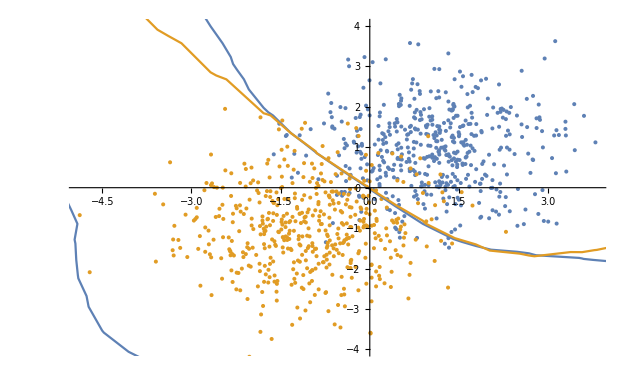

```mathematica
Show[ListPlot[{XT1,XT2},PlotRange->{-4,4}],ContourPlot[{θ.x1x2==0,θ1.x1x2==0},{x1,-50,50},{x2,-50,50}]]
```